```mathematica
T=Table[NumberOfGraphs[n], {n, 1, 25}];
```

{1,2,4,11,34,156,1044,12346,274668,12005168,1018997864,165091172592,50502031367952,29054155657235488,31426485969804308768,64001015704527557894928,245935864153532932683719776,1787577725145611700547878190848,24637809253125004524383007491432768,645490122795799841856164638490742749440,32220272899808983433502244253755283616097664,3070846483094144300637568517187105410586657814272,559946939699792080597976380819462179812276348458981632,195704906302078447922174862416726256004122075267063365754368,131331393569895519432161548405816890146389214706146483380458576384}

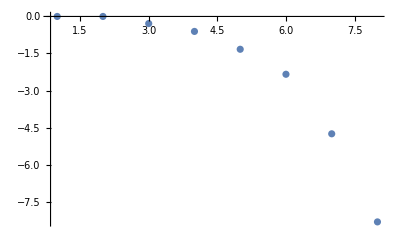

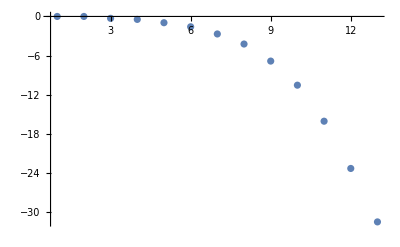

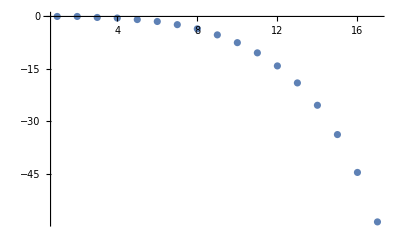

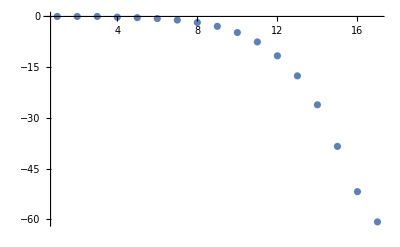

```mathematica
R34 = List[1, 2, 3, 6, 9, 15, 9, 3];
LenR34=Length[R34];
R34frac=Table[0, LenR34];
For [i=1, i<=LenR34, i++, 
R34frac[[i]]=Log[R34[[i]]/T[[i]]];
]
R35 = List[1, 2, 3, 7, 13, 32, 71, 179, 290, 313, 105, 12, 1];
LenR35=Length[R35];
R35frac=Table[0, LenR35];
For [i=1, i<=LenR35, i++, 
R35frac[[i]]=Log[R35[[i]]/T[[i]]];
]
R36=List[1, 2, 3, 7, 14, 37, 100, 356, 1407, 6657, 30395, 116792, 275086, 263520, 64732, 2576, 7];
LenR36=Length[R36];
R36frac=Table[0, LenR36];
For [i=1, i<=LenR36, i++, 
R36frac[[i]]=Log[R36[[i]]/T[[i]]];
]
R44 = List[1, 2, 4, 9, 24, 84, 362, 2079, 14701, 103706, 546356, 1449166, 1184231, 130816, 640, 2, 1];
LenR44=Length[R44];
R44frac = Table[0, LenR44];
For[i=1, i<=LenR44, i++,
R44frac[[i]]=Log[R44[[i]]/T[[i]]];
]
ListPlot[{R34frac}, PlotRange ->All]
ListPlot[{R35frac}, PlotRange ->All]
ListPlot[{R36frac}, PlotRange ->All]
ListPlot[{R44frac}, PlotRange->All]
```

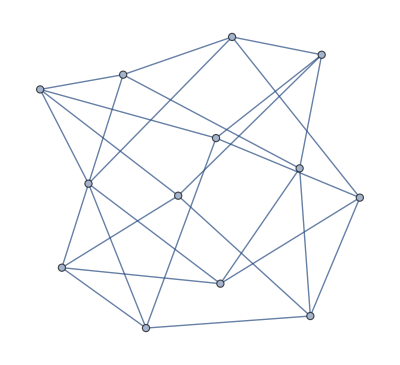

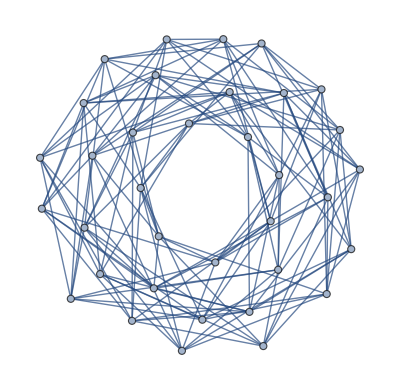

```mathematica
G=Import["Grafencollectie//r35_13.g6"]
H=Import["Grafencollectie//r39_35.g6"]
```